```mathematica
R = 53/10 * 10^3;R1=R;R2:=α*R1;R3=R1;R4=R1; C1=10^-5; C2=C1;RC1:=1/(I ω C1); RC2:=1/(I ω C2);
R3RC1 := (RC1*R3)/(RC1+R3);
kk = R3RC1/(R3RC1+R4+RC2);
```

```mathematica
KK=1/(R1*(kk/R1+(kk-1)/R2))//Simplify
```

(α (-1000000 ⅈ+159000 ω+2809 ⅈ ω^2))/(1000000 ⅈ+53000 (-2+α) ω-2809 ⅈ ω^2)

```mathematica
K[ω_, α_]:=(α (-1000000 I+159000 ω+2809 I ω^2))/(1000000 I+53000 (-2+α) ω-2809 I ω^2);
```

```mathematica
α = 18/10;
```

```mathematica
ω0 = NArgMax[{Abs[K[ω, α]], ω>0}, ω];
Kmax = Abs[K[ω0, α]];
NSolve[{Kmax/√2== Evaluate[Abs[K[ω, α]]]&&ω∈Reals&&ω>0}, ω]
```

{{ω→17.0676},{ω→20.8581}}

```mathematica
LogPlot[{Abs[K[ω, α]],Kmax/(√2)}, {ω, 0, 100}]
```

```mathematica
Kmax
```

27.

```mathematica
Kmax/√2
```

19.0919

```mathematica
Log[10,Kmax - Kmax/√2]
```

0.898073

```mathematica
α = 15/10;
```

```mathematica
ω0 = NArgMax[{Abs[K[ω, α]], ω>0}, ω];
Kmax = Abs[K[ω0, α]];
NSolve[{Kmax/√2== Evaluate[Abs[K[ω, α]]]&&ω∈Reals&&ω>0}, ω]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ω→14.6285},{ω→24.336}}

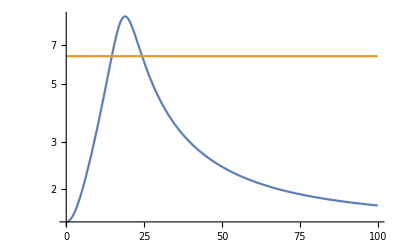

```mathematica
LogPlot[{Abs[K[ω, α]],Kmax/(√2)}, {ω, 0, 100}]
```

```mathematica
α = 12/10;
```

```mathematica
ω0 = NArgMax[{Abs[K[ω, α]], ω>0}, ω];
Kmax = Abs[K[ω0, α]];
NSolve[{Kmax/√2== Evaluate[Abs[K[ω, α]]]&&ω∈Reals&&ω>0}, ω]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ω→12.4036},{ω→28.7013}}

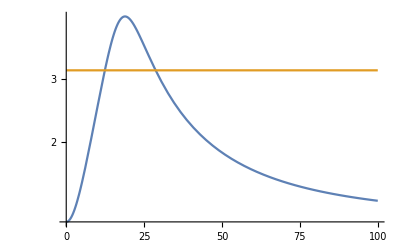

```mathematica
LogPlot[{Abs[K[ω, α]],Kmax/(√2)}, {ω, 0, 100}]
```

```mathematica
20*Log[10, 1/(√2)] // N
```

-3.0103